```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3, 1<x≤2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3, 2<x≤3}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
I3=f[3]
```

1+c01+c02+c03

c11+c12+c13

c21+c22+c23

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+2]+f[x+1]+f[x]+f[x-1]+f[x-2]+f[x-3],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-2f[x+2]-f[x+1]+f[x-1]+2f[x-2]+3f[x-3],x>0&&x<1],x]
```

{2+c01+c02+c03+c11+c12+c13+c21+c22+c23,-2 c02-3 c03-2 c12-3 c13-2 c22-3 c23,2 c02+3 c03+2 c12+3 c13+2 c22+3 c23}

{1+c01+c02+c03+2 c11+2 c12+2 c13+3 c21+3 c22+3 c23,-c01-2 c02-3 c03-3 c11-4 c12-6 c13-5 c21-6 c22-9 c23,c02+3 c03+c12+6 c13+c22+9 c23,-c03-3 c13-5 c23}

```mathematica
(*Smoothness*)
Df=Simplify[D[f[x],x],x>0]/.Abs'[x]->1
c01+x (2 c02+3 c03 x)/.x->1
c11+(2 c12+3 c13 (-1+x)) (-1+x)/.x->1
c11+(2 c12+3 c13 (-1+x)) (-1+x)/.x->2
c21+(2 c22+3 c23 (-2+x)) (-2+x)/.x->2
c21+(2 c22+3 c23 (-2+x)) (-2+x)/.x->3
```

Piecewise[{{c01+x (2 c02+3 c03 x), x≤1}, {c11+(2 c12+3 c13 (-1+x)) (-1+x), 1<x≤2}, {c21+(2 c22+3 c23 (-2+x)) (-2+x), 2<x≤3}, {0, True}}]

c01+2 c02+3 c03

c11

c11+2 c12+3 c13

c21

c21+2 c22+3 c23

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	I3==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0,
	c01==0,
	c01+2 c02+3 c03==c11,
	c11+2 c12+3 c13==c21,
	c21+2 c22+3 c23==0
	},
	{c01,c02,c03,c11,c12,c13,c21,c22,c23}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c03→-1-c02,c11→-3-c02,c12→19/4+(3 c02)/2,c13→-7/4-c02/2,c21→5/4+c02/2,c22→-5/2-c02,c23→5/4+c02/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>2&&y<3],
	Simplify[SumF1,x>-2&&x<-1&&y>3&&y<4]
}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1a6}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]],
	FullSimplify[D[SumF1a5,{{x,y}}]],
	FullSimplify[D[SumF1a6,{{x,y}}]]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-2&&y<-1],
	Simplify[SumF1,x>3&&x<4&&y>-3&&y<-2]
}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5,DSumF1b6}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]],
	FullSimplify[D[SumF1b5,{{x,y}}]],
	FullSimplify[D[SumF1b6,{{x,y}}]]
}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1a6}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-2^-1 (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_3^4 ∫_-2^-1 (DSumF1a6.{1,1})^2 ⅆxⅆy]
}];
{Err1b1,Err1b2,Err1b3,Err1b4,Err1b5,Err1b6}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_3^4 (DSumF1b5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-3^-2 ∫_3^4 (DSumF1b6.{1,1})^2 ⅆxⅆy]
}];
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1a6+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5+Err1b6];
```

```mathematica
Err=FullSimplify[Err1/.φ->1/2]
DErr=FullSimplify[D[Err,{{c02}}]];
H=FullSimplify[D[Err,{{c02},2}]];
Sols=RootReduce[Solve[DErr==0,{c02}]];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

(92669325+8 c02 (14686668+c02 (6527619+2 c02 (582860+37381 c02))))/25804800

1 | 0.0575003 | True
2 | 0.692089-0.0754737 ⅈ | False
3 | 0.692089+0.0754737 ⅈ | False

```mathematica
Sols[[1]]
```

{c02→Root[7343334+6527619 #1+1748580 #1^2+149524 #1^3&,1]}

{c01→0.,c03→1.06787,c11→-0.932133,c12→1.6482,c13→-0.716067,c21→0.216067,c22→-0.432133,c23→0.216067,c02→-2.06787}

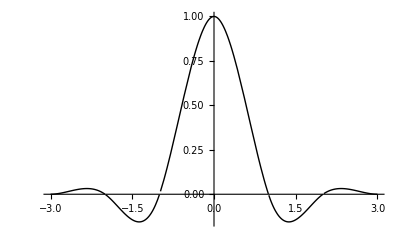

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```